```mathematica
pdf={{"-",120332},{"0",24320},{"1",32426},{"2",29841},{"3",19390},{"4",18611},{"5",13899},{"6",12393},{"7",11609},{"8",15448},{"9",12737},{"_",255},{"A",930794},{"B",245537},{"C",373911},{"D",327954},{"E",1006366},{"F",169800},{"G",248782},{"H",258077},{"I",746503},{"J",56986},{"K",188342},{"L",477495},{"M",338951},{"N",618224},{"O",738512},{"P",282326},{"Q",20848},{"R",648487},{"S",667752},{"T",624012},{"U",335063},{"V",132085},{"W",130378},{"X",66844},{"Y",182189},{"Z",70884}};
pdf=SortBy[Map[{ToCharacterCode[Characters[#[[1]]][[1]]][[1]],(#[[2]])/Total[Transpose[pdf][[2]]]}&,pdf],#[[1]]&]//N;
Map[{FromCharacterCode[Floor[#[[1]]]],#[[2]]}&,pdf]
Entropy[pdf[[All,2]]]//N
Times@@Transpose[pdf]//Total
Mean[pdf[[All,1]]]
(%%)/%
```

{{-,0.0117991},{0,0.0023847},{1,0.00317953},{2,0.00292606},{3,0.00190129},{4,0.0018249},{5,0.00136287},{6,0.0012152},{7,0.00113832},{8,0.00151475},{9,0.00124893},{A,0.091269},{B,0.0240761},{C,0.0366638},{D,0.0321575},{E,0.0986792},{F,0.0166497},{G,0.0243943},{H,0.0253057},{I,0.0731983},{J,0.00558776},{K,0.0184679},{L,0.0468207},{M,0.0332358},{N,0.0606199},{O,0.0724148},{P,0.0276835},{Q,0.00204425},{R,0.0635874},{S,0.0654764},{T,0.0611875},{U,0.0328546},{V,0.0129516},{W,0.0127842},{X,0.00655439},{Y,0.0178645},{Z,0.00695053},{_,0.000025004}}

3.63759

74.8797

70.5263

1.06173

```mathematica
UniformSample=Function[{list,num},
If[num≥Length[list],
list,
list[[1;;;;Floor[Length[list]/num]]]
]
];
```

```mathematica
RandomSubsets=Function[{list,length,max},
If[Length[list]^length≤max,
Tuples[Table[list,{length}]],
Table[
RandomChoice[list,length],{max}]
]
];
RandomSubsetsC=Compile[{{list,_Real,2},{length,_Integer},{max,_Integer}},RandomSubsets[list,length,max]];
```

```mathematica
ObservationsL=Function[{list,n,max},
SortBy[
Module[{t={{0.0},{0.0}},pt=0.0},
t=Table[
{Norm[#[[1]]],Times@@#[[2]]}&[Transpose[RandomChoice[list,n]]],
{max}
];
pt=t[[All,2]]//Total;
Map[{#[[1]],(#[[2]])/pt}&,t]
],
#[[1]]&
]
];
ObservationsLC=Compile[{{list,_Real,2},{n,_Integer},{max,_Integer}},ObservationsL[list,n,max],RuntimeOptions->"Speed"];
```

```mathematica
ListInterpolation2D=Function[{l},
Module[{lix,liy},
{lix,liy}=Map[ListInterpolation[#,{{0,1}}]&,Transpose[l]];
Function[{t},
liy[lix[t]]
]
]
];
```

```mathematica
cv=ParallelTable[ObservationsLC[pdf,i,300000],{i,1,100}];//AbsoluteTiming
```

{42.67044,Null}

```mathematica
ev=Map[Total[Times@@Transpose[#]]&,cv];//AbsoluteTiming
av=Map[Mean,cv][[All,1]];//AbsoluteTiming
```

{1.7491,Null}

{0.58903,Null}

74.3039 √x

71.8527 √x

1.03411

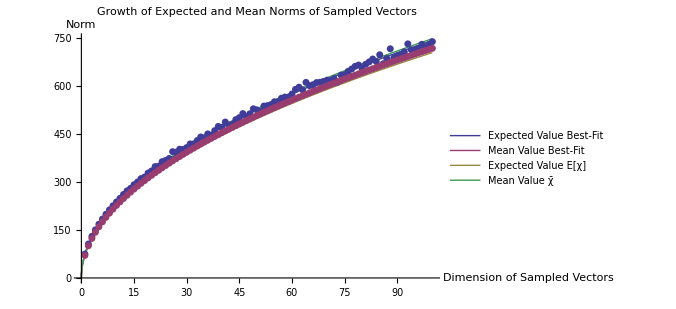

```mathematica
Fit[ev,{√y},y]/.y->x
Fit[av,{√y},y]/.y->x
Limit[(Fit[ev,{√y},y]/.y->x)/(Fit[av,{√y},y]/.y->x),x->∞]
Show[Plot[{Fit[ev,{√y},y]/.y->x,Fit[av,{√y},y]/.y->x,Mean[pdf[[All,1]]] √x,Total[Times@@Transpose[pdf]] √x},{x,0,Length[ev]},PlotStyle->Thick,PlotLegends->LineLegend[{"Expected Value\nBest-Fit","Mean Value\nBest-Fit","Expected Value\nE[χ]","Mean Value\nχ̄"}]],ListPlot[{ev,av},PlotStyle->PointSize[0.01]],ImageSize->500,PlotLabel->"Growth of Expected and Mean\nNorms of Sampled Vectors",AxesLabel->{"Dimension of\nSampled Vectors","Norm"}]
```

```mathematica
acv=Map[Transpose[{(#[[All,1]])/Max[#[[All,1]]],Accumulate[#[[All,2]]]}]&,cv];//AbsoluteTiming
fitsP=ParallelMap[FindFit[#,1/2 Erfc[(-y+μ)/(√2 σ)],{μ,σ},y]&,acv[[1;;100]]];//AbsoluteTiming
fits=1/2 Erfc[(-x+μ)/(√2 σ)]/.fitsP;
```

{3.19818,Null}

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{206.88785,Null}

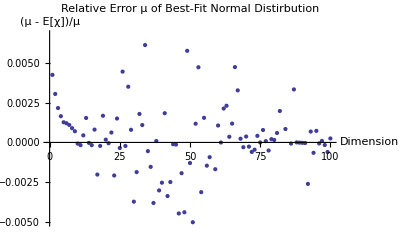

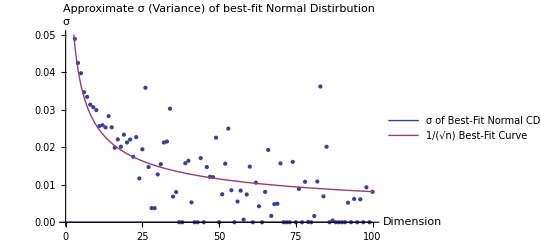

```mathematica
ListPlot[
{(Map[Max[#[[All,1]]]&,cv][[1;;Length[fitsP]]]Transpose[fitsP/.Rule->List][[1,All,2]]-ev[[1;;Length[fitsP]]])/(Map[Max[#[[All,1]]]&,cv][[1;;Length[fitsP]]]Transpose[fitsP/.Rule->List][[1,All,2]])}
,PlotLabel->"Relative Error μ of Best-Fit\nNormal Distirbution",AxesLabel->{"Dimension","(μ - E[χ])/μ"}]
Show[
{ListPlot[Transpose[fitsP/.Rule->List][[2,All,2]],PlotRange->{0,0.05}],
Plot[{0,Fit[Transpose[fitsP/.Rule->List][[2,All,2]],{1/(√y)},y]/.y->x},{x,0,Length[fitsP]},PlotRange->{0,0.05},PlotLegends->{"σ of Best-Fit Normal CDF","1/(√n) Best-Fit Curve"}]},PlotLabel->"Approximate σ (Variance) of best-fit\nNormal Distirbution",AxesLabel->{"Dimension","σ"}
]
```

```mathematica
Plot[fits,{x,0,1},PlotStyle->Table[Hue[(0.75i)/Length[cv]],{i,0,Length[cv]-1}]]
```

General::unfl: Underflow occurred in computation.

```mathematica
mse=ParallelTable[Total[Map[(#[[2]]-fits[[i]]/.x->#[[1]])^2&,acv[[i]]]]/Length[acv[[i]]],{i,1,30}]
```

Part::partw: Part 21 of {1/2\ Erfc[7.60528\ (0.78716  - x)], 1/2\ Erfc[10.7165\ (0.811272  - x)], 1/2\ Erfc[14.8734\ (0.838359  - x)], 1/2\ Erfc[14.4467\ (0.856741  - x)], « 12 », 1/2\ Erfc[33670.8\ (0.966454  - x)], 1/2\ Erfc[260519.\ (0.890205  - x)], 1/2\ Erfc[12.2144\ (0.908957  - x)], 1/2\ Erfc[12833.\ (0.931144  - x)]} does not exist.

Part::partw: Part 25 of {1/2\ Erfc[7.60528\ (0.78716  - x)], 1/2\ Erfc[10.7165\ (0.811272  - x)], 1/2\ Erfc[14.8734\ (0.838359  - x)], 1/2\ Erfc[14.4467\ (0.856741  - x)], « 12 », 1/2\ Erfc[33670.8\ (0.966454  - x)], 1/2\ Erfc[260519.\ (0.890205  - x)], 1/2\ Erfc[12.2144\ (0.908957  - x)], 1/2\ Erfc[12833.\ (0.931144  - x)]} does not exist.

Part::partw: Part 21 of {0.391264, 0.225311, 0.0529683, 0.0258328, 0.025489, 0.013712, « 8 », 2.07975×10^-80, 2.25215×10^-16, 2.15274447921263×10^-20683383, 2.39341127948079×10^-488294682, 0.00542953, 5.99518530193448×10^-2058448} does not exist.

Part::partw: Part 25 of {0.521682, 0.386362, 0.16588, 0.0937029, 0.127347, 0.0715033, « 8 », 1.23205×10^-51, 2.03882×10^-11, 2.78784428506758×10^-14947916, 8.42107545533862×10^-283024652, 0.0218706, 8.68868812930116×10^-1380468} does not exist.

Part::partw: Part 28 of {1/2\ Erfc[7.60528\ (0.78716  - x)], 1/2\ Erfc[10.7165\ (0.811272  - x)], 1/2\ Erfc[14.8734\ (0.838359  - x)], 1/2\ Erfc[14.4467\ (0.856741  - x)], « 12 », 1/2\ Erfc[33670.8\ (0.966454  - x)], 1/2\ Erfc[260519.\ (0.890205  - x)], 1/2\ Erfc[12.2144\ (0.908957  - x)], 1/2\ Erfc[12833.\ (0.931144  - x)]} does not exist.

Part::partw: Part 21 of {1/2\ Erfc[7.60528\ (0.78716  - x)], 1/2\ Erfc[10.7165\ (0.811272  - x)], 1/2\ Erfc[14.8734\ (0.838359  - x)], 1/2\ Erfc[14.4467\ (0.856741  - x)], « 12 », 1/2\ Erfc[33670.8\ (0.966454  - x)], 1/2\ Erfc[260519.\ (0.890205  - x)], 1/2\ Erfc[12.2144\ (0.908957  - x)], 1/2\ Erfc[12833.\ (0.931144  - x)]} does not exist.

Part::partw: Part 25 of {1/2\ Erfc[7.60528\ (0.78716  - x)], 1/2\ Erfc[10.7165\ (0.811272  - x)], 1/2\ Erfc[14.8734\ (0.838359  - x)], 1/2\ Erfc[14.4467\ (0.856741  - x)], « 12 », 1/2\ Erfc[33670.8\ (0.966454  - x)], 1/2\ Erfc[260519.\ (0.890205  - x)], 1/2\ Erfc[12.2144\ (0.908957  - x)], 1/2\ Erfc[12833.\ (0.931144  - x)]} does not exist.

Part::partw: Part 28 of {0.546035, 0.419772, 0.197455, 0.114701, 0.161497, 0.0922017, « 8 », 5.1306×10^-47, 1.31797×10^-10, 5.79627145606518×10^-13986440, 3.67856759468721×10^-251072978, 0.0275456, 1.49179959380684×10^-1269576} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Part::partw: Part 28 of {1/2\ Erfc[7.60528\ (0.78716  - x)], 1/2\ Erfc[10.7165\ (0.811272  - x)], 1/2\ Erfc[14.8734\ (0.838359  - x)], 1/2\ Erfc[14.4467\ (0.856741  - x)], « 12 », 1/2\ Erfc[33670.8\ (0.966454  - x)], 1/2\ Erfc[260519.\ (0.890205  - x)], 1/2\ Erfc[12.2144\ (0.908957  - x)], 1/2\ Erfc[12833.\ (0.931144  - x)]} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Part::partw: Part 21 of {0.391264, 0.225311, 0.0529683, 0.0258328, 0.025489, 0.013712, « 8 », 2.07975×10^-80, 2.25215×10^-16, 2.15274447921263×10^-20683383, 2.39341127948079×10^-488294682, 0.00542953, 5.99518530193448×10^-2058448} does not exist.

Part::partw: Part 21 of {0.481451, 0.333244, 0.121428, 0.06553, 0.082696, 0.0454307, 0.0163021, « 7 », 9.91273×10^-60, 7.95835×10^-13, 2.86591776542813×10^-16600682, 1.54169571598357×10^-339803721, 0.014681, 2.38654084118916×10^-1573172} does not exist.

Part::partw: Part 21 of {0.489527, 0.343684, 0.129605, 0.070584, 0.0905559, 0.0499379, « 8 », 4.67966×10^-58, 1.55253×10^-12, 1.13323969325797×10^-16261871, 1.48858167387343×10^-327986879, 0.0159342, 2.24085953337427×10^-1533469} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

$Aborted[]

```mathematica
msre=ParallelTable[Total[Map[((#[[2]]-fits[[i]]/.x->#[[1]])/(#[[2]]))^2&,acv[[i]]]]/Length[acv[[i]]],{i,1,30}]
```

{0.185103,1.,0.133723,0.114131,0.136141,0.154982,0.13864,0.0654411,0.182233,0.266196,0.260151,0.466853,0.14889,1.,1.,0.489388,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

```mathematica
k=5;
ListPlot[
acv[[1;;k]],Joined->True,PlotRange->{{0,1},{0,1}},PlotStyle->Map[{Thick,Darker[#]}&,Table[Hue[i/k],{i,0,k-1}]]]
```

No more memory available.
Mathematica kernel has shut down.
Try quitting other applications and then retry.

```mathematica
Plot[fits[[1;;k]],{x,0,1},PlotRange->{{0,1},{0,1}},PlotStyle->Map[{Dashed,Thick,Darker[#]}&,Table[Hue[i/k],{i,0,k-1}]]]
```

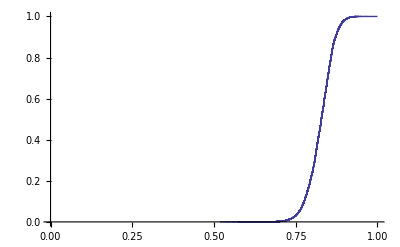

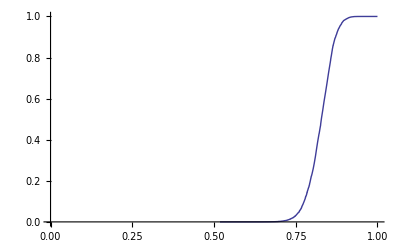

```mathematica
t=Map[Transpose[{(#[[All,1]])/(#[[All,1]]//Max),#[[All,2]]//Accumulate}]&,{cv[[5]]}][[1]];
ListPlot[t,Joined->True,AxesOrigin->{0,0}]
(*ListPlot[{Transpose[{t[[All,1]][[;;-2]],MeanFilter[Differences[t[[All,2]]],1000]}]},Joined->True,PlotRange->All]*)
lix=ListInterpolation[t[[All,1]],{{0,1}}];
liy=ListInterpolation[t[[All,2]],{{0,1}}];
ParametricPlot[{lix[u],liy[u]},{u,0,1},AxesOrigin->{0,0},AspectRatio->1/GoldenRatio]
```

## Testing Hypothesis : Convolution is for IID Observations = NOPE

ConditionalExpression[-√2 InverseErfc[2 p],0≤p≤1]

1/2 (1+Erf[p/2])

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

2 InverseErf[-1+2 #1]&

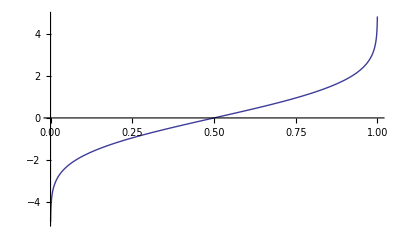

```mathematica
InverseCDF[NormalDistribution[0,1],p]
Integrate[(ⅇ^(-x^2/4))/(2 √π),{x,-∞,p}]
InverseFunction[1/2 (1+Erf[#/2])&]
Plot[2 InverseErf[-1+2 p],{p,0,1}]
```

(ⅇ^(-x^2/4))/(2 √π)

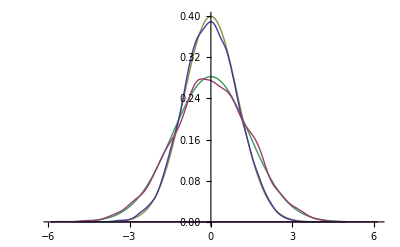

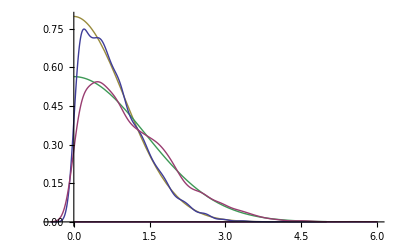

```mathematica
Convolve[PDF[NormalDistribution[0,1],y],PDF[NormalDistribution[0,1],y],y,x]
pts1=-√2 InverseErfc[2 x]/.x->Table[RandomReal[{0,1}],{5000}];
pts2=2 InverseErf[-1+2 x]/.x->Table[RandomReal[{0,1}],{5000}];
Show[Plot[{0,0,PDF[NormalDistribution[0,1],x],(ⅇ^(-x^2/4))/(2 √π)},{x,-5,5},PlotRange->All],SmoothHistogram[{pts1,pts2}]]
Show[Plot[{0,0,2PDF[NormalDistribution[0,1],x],2(ⅇ^(-x^2/4))/(2 √π)},{x,0,5},PlotRange->All],SmoothHistogram[{Abs[pts1],Abs[pts2]}]]
```

```mathematica
Plot3D[PDF[NormalDistribution[0,1],x]PDF[NormalDistribution[0,1],y],{x,-5,5},{y,-5,5},PlotRange->All,PlotPoints->50]
```

-Graphics3D-

-Graphics3D-

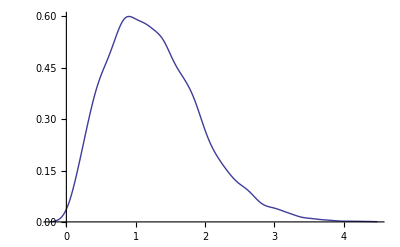

```mathematica
pts3={-√2 InverseErfc[2 x]/.x->Table[RandomReal[{0,1}],{5000}],-√2 InverseErfc[2 x]/.x->Table[RandomReal[{0,1}],{5000}]}//Transpose;
SmoothHistogram3D[pts3]
SmoothHistogram[Map[Norm,pts3]]
```

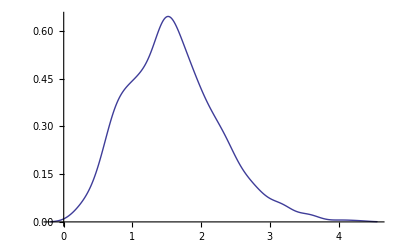

```mathematica
pts4={-√2 InverseErfc[2 x]/.x->Table[RandomReal[{0,1}],{1000}],-√2 InverseErfc[2 x]/.x->Table[RandomReal[{0,1}],{1000}],-√2 InverseErfc[2 x]/.x->Table[RandomReal[{0,1}],{1000}]}//Transpose;
SmoothHistogram[Map[Norm,pts4]]
```

```mathematica
pts5={-√2 InverseErfc[2 x]/.x->Table[RandomReal[{0,1}],{1000}],-√2 InverseErfc[2 x]/.x->Table[RandomReal[{0,1}],{1000}],-√2 InverseErfc[2 x]/.x->Table[RandomReal[{0,1}],{1000}],-√2 InverseErfc[2 x]/.x->Table[RandomReal[{0,1}],{1000}]}//Transpose;
```

```mathematica
pts6={-√2 InverseErfc[2 x]/.x->Table[RandomReal[{0,1}],{1000}],-√2 InverseErfc[2 x]/.x->Table[RandomReal[{0,1}],{1000}],-√2 InverseErfc[2 x]/.x->Table[RandomReal[{0,1}],{1000}],-√2 InverseErfc[2 x]/.x->Table[RandomReal[{0,1}],{1000}],-√2 InverseErfc[2 x]/.x->Table[RandomReal[{0,1}],{1000}]}//Transpose;
```

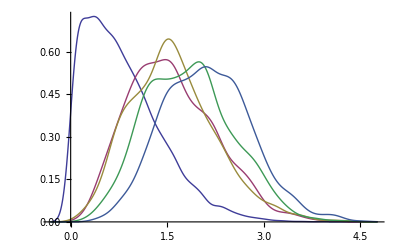

```mathematica
SmoothHistogram[{Abs[pts1],Map[Norm,pts3],Map[Norm,pts4],Map[Norm,pts5],Map[Norm,pts6]}]
```

```mathematica
s={a,b,c,d,e,f,g,h}
Total[s]^2//Expand
```

{a,b,c,d,e,f,g,h}

a^2+2 a b+b^2+2 a c+2 b c+c^2+2 a d+2 b d+2 c d+d^2+2 a e+2 b e+2 c e+2 d e+e^2+2 a f+2 b f+2 c f+2 d f+2 e f+f^2+2 a g+2 b g+2 c g+2 d g+2 e g+2 f g+g^2+2 a h+2 b h+2 c h+2 d h+2 e h+2 f h+2 g h+h^2

{6.45537,Null}

{6.42037,Null}